## Contour Plot

## Import data and Settings

```mathematica
SetDirectory["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/climate_social"];
```

```mathematica
(* Heat data for delta and kappa variation (different bin sizes) *)
```

```mathematica
betaKappaData=Import["export_data/temp_anomaly/contour_beta_kappa2.dat"];
```

### Settings

```mathematica
imgs=200;
```

## Colour Contour

```mathematica
(* remove elements outside of range *)
dataFilt = Cases[betaKappaData,{x_,y_,_}/;(0.5<=x<=1.5) && (0.02<=y<=0.2)];
```

```mathematica
dataFilt//Dimensions
```

{209,3}

```mathematica
betaKappaData//Dimensions
```

{380,3}

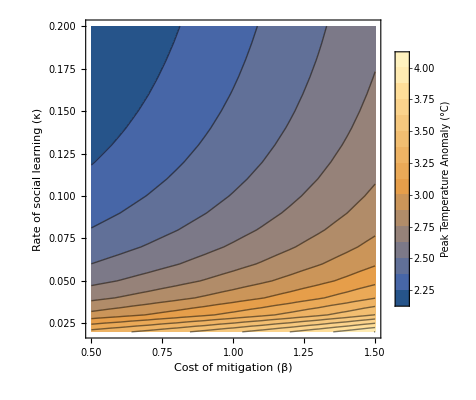

```mathematica
heatMap=ListContourPlot[dataFilt,InterpolationOrder->1,
PlotLegends->Placed[BarLegend[Automatic,LegendLabel->Style["Peak\nTemperature\nAnomaly (°C)",12]],Right],
FrameLabel->{"Cost of mitigation (β)","Rate of social learning (κ)"},LabelStyle->14,
PlotRange->{{0.5,1.5},{0.02,0.2},All},
Contours->Range[2.25,4,0.125]
]
```

```mathematica
Export["figures/fig_contour_beta_kappa2.png",heatMap,ImageResolution->100];
```

## Black and White with labelling

```mathematica
contourNumbers={2.25,2.5,2.75,3,3.25,3.5,3.75,4,4.25};
```

```mathematica
contourLabels=ToString[#]<>"°C" & /@contourNumbers
```

{2.25°C,2.5°C,2.75°C,3°C,3.25°C,3.5°C,3.75°C,4°C,4.25°C}

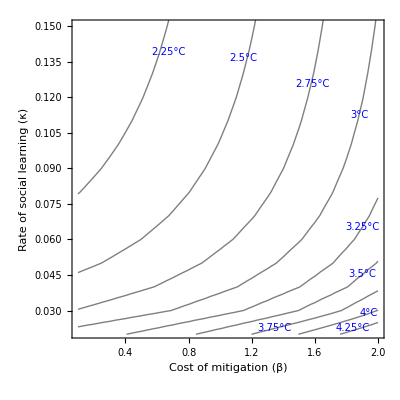

```mathematica
contourPositions={{0.31,0.9},{0.55,0.88},{0.77,0.8},{0.92,0.7},{0.93,0.35},{0.93,0.2},{0.65,0.03},{0.95,0.08},{0.9,0.03}};

bwContour=ListContourPlot[betaKappaData,
LabelStyle->14,
ContourShading->None,
FrameLabel->{"Cost of mitigation (β)","Rate of social learning (κ)"},
PlotRange->{All,{0.021,0.15},All},
InterpolationOrder->1,
Contours->Range[2,4.25,0.25],
Epilog->{Text[Style[#1,Blue,10],Scaled[#2]]&@@@Transpose[{contourLabels,contourPositions}]}
]
```

```mathematica
(*Export["figures/fig_countour_beta_kappa_bw.png",bwContour,ImageResolution->100];*)
```